```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadTARCER=True;
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

TARCER 2.0, for description see the preprint hep-ph/9801383 at arxiv.org.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

0

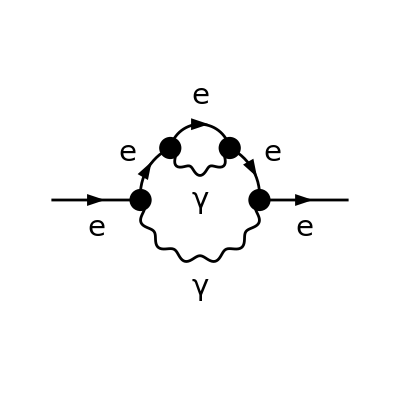

```mathematica
(* ::Subsection::*)
(*Electron self-energy*)


topsSE=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
diagsSE=InsertFields[topsSE,{F[2,{1}]}->{F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{V[2|3],S[_],U[_],F[1|3|4]}];
Paint[DiagramExtract[diagsSE,{5}],ColumnsXRows->{3,1},SheetHeader->False,Numbering->None,ImageSize->{768,256}];
```

```mathematica
(* ::Text::*)
(*First of all we need to generate the amplitudes and convert them into FeynCalc notation.We choose l1 and l2 to be the loop momenta and p the external momentum*)


ampsSE=FCFAConvert[CreateFeynAmp[DiagramExtract[diagsSE,{5}],Truncated->True,PreFactor->-1,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l1,l2},DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,SMP->True,LorentzIndexNames->{μ}]//ReplaceAll[#,SMP["m_e"]->0]&//Contract//FCTraceFactor


(* ::Text::*)
(*Calculation of the Dirac trace,tensor reduction and simplification of the Dirac algebra*)


AbsoluteTiming[ampsSE1=(ampsSE/.DiracTrace->Tr)//FCMultiLoopTID[#,{l1,l2}]&//DiracSimplify]


(* ::Text::*)
(*Simplification of the loop integrals using shifts in the loop momenta*)


ampsSE2=ampsSE1//FDS[#,l1,l2]&


(* ::Text::*)
(*IBP-Reduction using FIRE*)


ampsSE3=FIREBurn[ampsSE2,{l1,l2},{p}]//FDS[#,l1,l2]&


(* ::Text::*)
(*Nicer form*)


ampsSE4=ampsSE3//Collect2[#,{FeynAmpDenominator},Factoring->FullSimplify]&


(* ::Text::*)
(*This is Sigma_2V(p^2) up to the 1/(2Pi)^2D prefactor*)


resSE=Cancel[ampsSE4/(-I FCI[(GSD[p])])]//FullSimplify


(* ::Subsection::*)
(*Check with the literature*)


(* ::Text::*)
(*Check with Eq.5.51 from Grozin's Lectures on QED and QCD (hep-ph/0508242)*)


resGrozinSE=FCI[SMP["e"]^4(D-2)(2(D-2)/(D-6)(1/SPD[p,p])FAD[l1,l1-l2,l2-p]-1/4((D-2)(GaugeXi[A])^2+D-6)FAD[l1,l2,l1-p,l2-p]+(1/2)(D-3)/(D-4)((3D-8)(GaugeXi[A])^2-D-4)(1/SPD[p,p])FAD[l1,l1-l2,l2-p])]//Cancel//FullSimplify;
```

(ⅈ e^4 ξ_A (γ·l1).(γ·(p-l1)).γ^Lor4.(γ·l2).γ^Lor4.(γ·(p-l1)).(γ·l1))/(l1^2.l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(ⅈ e^4 ξ_A γ^μ.(γ·(p-l1)).(γ·(-l1+l2+p)).(γ·l2).(γ·(l1-l2-p)).(γ·(p-l1)).γ^μ)/(l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)-(ⅈ e^4 (1-ξ_A)^2 (γ·l1).(γ·(p-l1)).(γ·(-l1+l2+p)).(γ·l2).(γ·(l1-l2-p)).(γ·(p-l1)).(γ·l1))/(l1^2.l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)+(ⅈ e^4 γ^μ.(γ·(p-l1)).γ^Lor4.(γ·l2).γ^Lor4.(γ·(p-l1)).γ^μ)/(l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(ⅈ e^4 (γ·l1).(γ·(p-l1)).γ^Lor4.(γ·l2).γ^Lor4.(γ·(p-l1)).(γ·l1))/(l1^2.l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)+(ⅈ e^4 γ^μ.(γ·(p-l1)).(γ·(-l1+l2+p)).(γ·l2).(γ·(l1-l2-p)).(γ·(p-l1)).γ^μ)/(l1^2.l2^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)

{27.6485,(ⅈ γ·p ξ_A^2 e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(ⅈ γ·p ξ_A^2 e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)-(ⅈ γ·p ξ_A^2 e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(ⅈ D γ·p ξ_A^2 e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)-(ⅈ D γ·p ξ_A^2 e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ D γ·p ξ_A^2 e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)-(ⅈ γ·p ξ_A^2 e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 p^4 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(ⅈ γ·p ξ_A^2 p^4 e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(ⅈ γ·p ξ_A^2 p^4 e^4)/(l2^2.l1^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 p^4 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p p^4 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(ⅈ γ·p p^4 e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(ⅈ γ·p p^4 e^4)/(l2^2.l1^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)+(ⅈ γ·p p^4 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A p^4 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)+(2 ⅈ γ·p ξ_A p^4 e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)+(2 ⅈ γ·p ξ_A p^4 e^4)/(l2^2.l1^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A p^4 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(2 ⅈ γ·p ξ_A^2 (l1·p) p^4 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p ξ_A^2 (l1·p) p^4 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(2 ⅈ γ·p (l1·p) p^4 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p (l1·p) p^4 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(4 ⅈ γ·p ξ_A (l1·p) p^4 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(4 ⅈ γ·p ξ_A (l1·p) p^4 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(ⅈ γ·p e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)-(ⅈ γ·p e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(ⅈ D γ·p e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)-(ⅈ D γ·p e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ D γ·p e^4)/(2 l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(ⅈ γ·p e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(ⅈ D^3 γ·p e^4)/(2 (D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)-(2 ⅈ D^2 γ·p e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)+(7 ⅈ D γ·p e^4)/(2 (D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)-(2 ⅈ γ·p e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)-(2 ⅈ γ·p ξ_A e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)+(2 ⅈ γ·p ξ_A e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-p)^2)+(2 ⅈ D γ·p ξ_A e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A e^4)/((D-1) l1^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(2 ⅈ D γ·p ξ_A e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(ⅈ D γ·p ξ_A e^4)/(2 l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(ⅈ D^2 γ·p ξ_A e^4)/(2 (D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)-(ⅈ D γ·p ξ_A e^4)/(2 (D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-l2)^2)+(2 ⅈ γ·p ξ_A^2 (l1·l2) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(2 ⅈ γ·p (l1·l2) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ D^3 γ·p (l1·l2) e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)+(10 ⅈ D^2 γ·p (l1·l2) e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(16 ⅈ D γ·p (l1·l2) e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)+(8 ⅈ γ·p (l1·l2) e^4)/((D-1) l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(4 ⅈ γ·p ξ_A (l1·l2) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p ξ_A^2 (l1·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p ξ_A^2 (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)+(ⅈ D γ·p ξ_A^2 (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(ⅈ γ·p ξ_A^2 (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)-(2 ⅈ γ·p (l1·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)+(2 ⅈ D γ·p (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(4 ⅈ γ·p (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(ⅈ D^2 γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(4 ⅈ D γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(3 ⅈ γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(ⅈ D γ·p (l1·p) e^4)/(l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(2 ⅈ γ·p (l1·p) e^4)/(l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(ⅈ D^3 γ·p (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)+(4 ⅈ D^2 γ·p (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)-(5 ⅈ D γ·p (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)+(2 ⅈ γ·p (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)+(ⅈ γ·p (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(4 ⅈ γ·p ξ_A (l1·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(4 ⅈ γ·p ξ_A (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)-(2 ⅈ D γ·p ξ_A (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(4 ⅈ γ·p ξ_A (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(ⅈ D^2 γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(5 ⅈ D γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(4 ⅈ γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ D γ·p ξ_A (l1·p) e^4)/(l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A (l1·p) e^4)/(l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(ⅈ D^2 γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)-(3 ⅈ D γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)+(2 ⅈ γ·p ξ_A (l1·p) e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2)-(2 ⅈ γ·p ξ_A (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2)+(ⅈ γ·p ξ_A^2 (l2·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(ⅈ D γ·p (l2·p) e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(2 ⅈ γ·p (l2·p) e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2)+(ⅈ D γ·p (l2·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)-(ⅈ γ·p (l2·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(ⅈ D^2 γ·p (l2·p) e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(4 ⅈ D γ·p (l2·p) e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)+(4 ⅈ γ·p (l2·p) e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2)-(ⅈ D γ·p ξ_A (l2·p) e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2)+(2 ⅈ γ·p ξ_A (l2·p) e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(ⅈ D γ·p ξ_A (l2·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)-(ⅈ D γ·p p^2 e^4)/(2 l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)+(ⅈ γ·p p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)+(ⅈ D γ·p ξ_A p^2 e^4)/(2 l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)-(ⅈ γ·p ξ_A p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2)-(2 ⅈ D γ·p (l1·p) p^2 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(4 ⅈ γ·p (l1·p) p^2 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(2 ⅈ D^2 γ·p (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(6 ⅈ D γ·p (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(4 ⅈ γ·p (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(2 ⅈ D γ·p (l1·p) p^2 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(4 ⅈ γ·p (l1·p) p^2 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(2 ⅈ D γ·p ξ_A (l1·p) p^2 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(4 ⅈ γ·p ξ_A (l1·p) p^2 e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ D^2 γ·p ξ_A (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)+(6 ⅈ D γ·p ξ_A (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(4 ⅈ γ·p ξ_A (l1·p) p^2 e^4)/((D-1) l2^2.l2^2.l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2)-(2 ⅈ D γ·p ξ_A (l1·p) p^2 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)+(4 ⅈ γ·p ξ_A (l1·p) p^2 e^4)/(l2^2.l2^2.l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2)-(ⅈ D γ·p (l2·p) p^2 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(2 ⅈ γ·p (l2·p) p^2 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)+(ⅈ D γ·p (l2·p) p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)-(2 ⅈ γ·p (l2·p) p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)+(ⅈ D γ·p ξ_A (l2·p) p^2 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)-(2 ⅈ γ·p ξ_A (l2·p) p^2 e^4)/(l1^2.l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2)-(ⅈ D γ·p ξ_A (l2·p) p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)+(2 ⅈ γ·p ξ_A (l2·p) p^2 e^4)/(l2^2.l1^2.(l1-p)^2.(l1-p)^2.(-l1+l2+p)^2.(-l1+l2+p)^2)-(2 ⅈ γ·p ξ_A^2 (l1·p)^2 e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(2 ⅈ γ·p (l1·p)^2 e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(4 ⅈ γ·p ξ_A (l1·p)^2 e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(ⅈ D^2 γ·p e^4)/(2 l1^2.(l2-p)^2.(l1-l2)^2 p^2)+(2 ⅈ D γ·p e^4)/(l1^2.(l2-p)^2.(l1-l2)^2 p^2)-(2 ⅈ γ·p e^4)/(l1^2.(l2-p)^2.(l1-l2)^2 p^2)+(ⅈ D γ·p ξ_A^2 (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(ⅈ γ·p ξ_A^2 (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(ⅈ γ·p ξ_A^2 (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(ⅈ γ·p ξ_A^2 (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2 p^2)-(ⅈ D^2 γ·p (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(4 ⅈ D γ·p (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(3 ⅈ γ·p (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(ⅈ D γ·p (l1·p) e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2 p^2)+(2 ⅈ γ·p (l1·p) e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2 p^2)+(ⅈ D^3 γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2 p^2)-(5 ⅈ D^2 γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2 p^2)+(8 ⅈ D γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2 p^2)-(4 ⅈ γ·p (l1·p) e^4)/((D-1) l2^2.l1^2.(l2-p)^2.(l1-l2)^2 p^2)-(ⅈ γ·p (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(ⅈ γ·p (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2 p^2)+(ⅈ D^2 γ·p ξ_A (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(5 ⅈ D γ·p ξ_A (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(4 ⅈ γ·p ξ_A (l1·p) e^4)/((D-1) l1^2.(l2-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)+(ⅈ D γ·p ξ_A (l1·p) e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2 p^2)-(2 ⅈ γ·p ξ_A (l1·p) e^4)/(l1^2.(l2-p)^2.(l2-p)^2.(l1-l2)^2 p^2)+(2 ⅈ γ·p ξ_A (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-l2)^2.(l1-l2)^2 p^2)-(2 ⅈ γ·p ξ_A (l1·p) e^4)/(l2^2.(l1-p)^2.(l1-p)^2.(l1-l2)^2 p^2)+(2 ⅈ γ·p ξ_A^2 (l1·p) (l2·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2 p^2)+(2 ⅈ γ·p (l1·p) (l2·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2 p^2)-(4 ⅈ γ·p ξ_A (l1·p) (l2·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2 p^2)}

-(ⅈ γ·p (ξ_A-1)^2 e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(ⅈ (D-2) γ·p (ξ_A-1) e^4)/(2 l1^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(ⅈ γ·p (D^2-ξ_A D-3 D+2 ξ_A^2-2 ξ_A+4) e^4)/(2 l1^2.l2^2.(l1-l2)^2.(l1-p)^2)+(2 ⅈ γ·p (ξ_A-1)^2 (l1·l2) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(2 ⅈ γ·p (ξ_A-1)^2 (l1·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)+(ⅈ γ·p (ξ_A-1)^2 (l1·p) e^4)/(l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(ⅈ (D-2)^2 γ·p (l1·p) e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2)-(ⅈ (D-2) γ·p (D-ξ_A-1) (l1·p) e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2)-(ⅈ (D-2) γ·p (ξ_A-1) (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2)-(ⅈ (D-2) γ·p (ξ_A-1) (l1·p) e^4)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2)-(ⅈ γ·p (D-ξ_A-1) (ξ_A-1) (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)-(ⅈ γ·p (ξ_A-1) (-D+ξ_A+1) (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2)-2 ⅈ (D-2)^2 γ·p (1/(2 l1^2.l2^2.(l1-l2)^2.(l1-p)^2)-(l1·p)/(l1^2.l2^2.l2^2.(l1-l2)^2.(l2-p)^2)) e^4+(ⅈ (D-2) γ·p (ξ_A-1) p^2 e^4)/(2 l1^2.l2^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2)-(2 ⅈ γ·p (ξ_A-1)^2 (l1·p)^2 e^4)/(l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2 p^2)-(ⅈ (D-2)^2 γ·p e^4)/(2 l1^2.(l1-l2)^2.(l2-p)^2 p^2)-(ⅈ γ·p (ξ_A-1)^2 (l1·p) e^4)/(l2^2.(l1-l2)^2.(l1-l2)^2.(l1-p)^2 p^2)+(ⅈ γ·p (ξ_A-1)^2 (l1·p) e^4)/(l2^2.(l1-l2)^2.(l1-p)^2.(l1-p)^2 p^2)+(ⅈ (D-2)^2 γ·p (l1·p) e^4)/(l1^2.l2^2.(l1-l2)^2.(l2-p)^2 p^2)+(ⅈ (D-2) γ·p (ξ_A-1) (l1·p) e^4)/(l1^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2 p^2)+(ⅈ γ·p (ξ_A-1) (D+ξ_A-3) (l1·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2 p^2)+(2 ⅈ γ·p (ξ_A-1)^2 (l1·p) (l2·p) e^4)/(l1^2.(l1-l2)^2.(l1-l2)^2.(l2-p)^2.(l2-p)^2 p^2)

FIREBurn: Processing integral 1 of 15; IBP-reduction done, timing: 3.162
FIREBurn: Processing integral 2 of 15; IBP-reduction done, timing: 2.273
FIREBurn: Processing integral 3 of 15; IBP-reduction done, timing: 1.865
FIREBurn: Processing integral 4 of 15; IBP-reduction done, timing: 1.869
FIREBurn: Processing integral 5 of 15; IBP-reduction done, timing: 1.894
FIREBurn: Processing integral 6 of 15; IBP-reduction done, timing: 1.913
FIREBurn: Processing integral 7 of 15; IBP-reduction done, timing: 1.946
FIREBurn: Processing integral 8 of 15; IBP-reduction done, timing: 1.872
FIREBurn: Processing integral 9 of 15; IBP-reduction done, timing: 1.847
FIREBurn: Processing integral 10 of 15; IBP-reduction done, timing: 1.838
FIREBurn: Processing integral 11 of 15; IBP-reduction done, timing: 1.960
FIREBurn: Processing integral 12 of 15; IBP-reduction done, timing: 2.013
FIREBurn: Processing integral 13 of 15; IBP-reduction done, timing: 2.237
FIREBurn: Processing integral 14 of 15; IBP-reduction done, timing: 1.821
FIREBurn: Processing integral 15 of 15; IBP-reduction done, timing: 1.885

(ⅈ (D-2) e^4 (2 D^2 ξ_A^2+D^2 ξ_A-10 D ξ_A^2-11 D ξ_A+12 ξ_A^2+24 ξ_A-2 D^2+17 D-32) γ·p)/(2 (D-4) p^2 l1^2.(l1-l2)^2.(l2-p)^2)-(ⅈ (D-2) e^4 (4 D^2 ξ_A^2+D^2 ξ_A-20 D ξ_A^2-11 D ξ_A+24 ξ_A^2+24 ξ_A-2 D^2+17 D-32) γ·p)/(2 (D-4) p^2 l1^2.(l1-l2)^2.(l2-p)^2)

-(ⅈ (D-3) (D-2)^2 e^4 ξ_A^2 γ·p)/((D-4) p^2 l1^2.(l1-l2)^2.(l2-p)^2)

((D-3) (D-2)^2 e^4 ξ_A^2)/((D-4) p^2 l1^2.(l1-l2)^2.(l2-p)^2)

```mathematica
tfiamp0=resSE//ToTFI[#,l1,l2,p]&;
SE=Simplify[TarcerRecurse[tfiamp0]]
```

((D-3) (D-2)^2 e^4 ξ_A^2 J_({1,0}{1,0}{1,0})^(D))/((D-4) p^2)